```mathematica
pHd=Show[Plot3D[pHdgd[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[pHerd[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEd=Show[Plot3D[pEdgd[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[pEerd[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

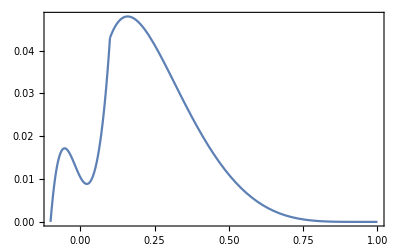
-Graphics-H_dx

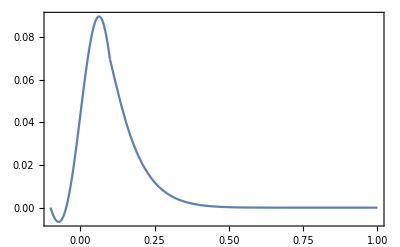
-Graphics-E_dx

```mathematica
pHd2d=Labeled[Show[Plot[pHdgd[x,1],{x,0.1,1},PlotRange->All],Plot[pHerd[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d",
"x"},{Left,Bottom},LabelStyle->24]
pEd2d=Labeled[Show[Plot[pEdgd[x,1],{x,0.1,1},PlotRange->All],Plot[Re[pEerd[x,1]],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d",
"x"},{Left,Bottom},LabelStyle->24]
```

```mathematica
pathH=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H3d-b-D.pdf"}];
Export[pathH,pHd]


pathE=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E3d-b-D.pdf"}];
Export[pathE,pEd]


pathH2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H2d-b-D.pdf"}];
Export[pathH2d,pHd2d]
pathE2d=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E2d-b-D.pdf"}];
Export[pathE2d,pEd2d]
```

C:\Users\DELL\Desktop\73diagram\H3d-b-D.pdf

C:\Users\DELL\Desktop\73diagram\E3d-b-D.pdf

C:\Users\DELL\Desktop\73diagram\H2d-b-D.pdf

C:\Users\DELL\Desktop\73diagram\E2d-b-D.pdf

```mathematica
.
```

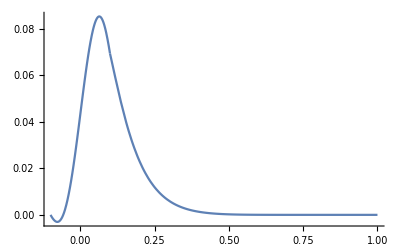

```mathematica
Show[Plot[pEdgd[x,1],{x,0.1,1},PlotRange->All],Plot[pEerd[x,1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Edgfnd[x_,t_]:=Edgf1d[x,t]+dEdgfd[x,t];
Eerfnd[x_,t_]:=Eerf1d[x,t]+dEerfd[x,t]+EerDf1d[x,t]+deEerDfd[x,t]
```

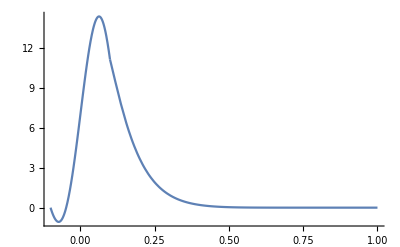

```mathematica
Show[Plot[-I*Edgfnd[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerfnd[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Show[Plot[I*(Edgf1d[x,-1]+dEdgfd[x,-1]),{x,0.1,1},PlotRange->All],Plot[I*Eerfnd[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

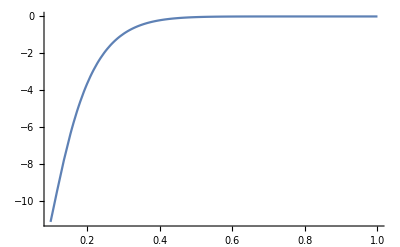

```mathematica
Plot[I*(Edgf1d[x,-1]+dEdgfd[x,-1]),{x,0.1,1},PlotRange->All]
```

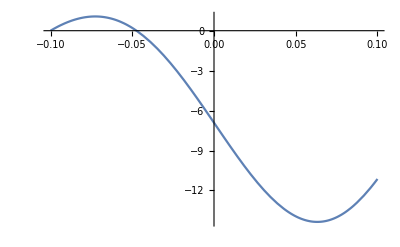

```mathematica
Plot[I*Eerfnd[x,-1],{x,-0.1,0.1},PlotRange->All]
```

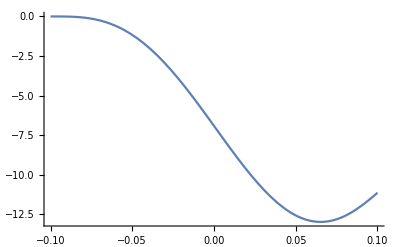

```mathematica
Plot[I*(Eerf1d[x,-1]+dEerfd[x,-1]),{x,-0.1,0.1},PlotRange->All]
```

```mathematica
EerDf1d[x,t]+deHerDfd[x,t]
```

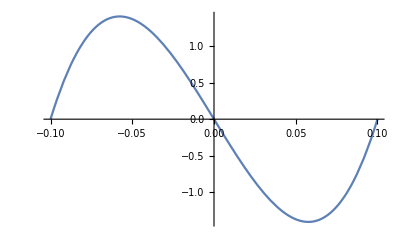

```mathematica
Plot[I*(EerDf1d[x,-1]+deEerDfd[x,-1]),{x,-0.1,0.1},PlotRange->All]
```

```mathematica
Plot[I*(EerDf1d[x,-1]),{x,-0.1,0.1},PlotRange->All]
```

-Graphics-

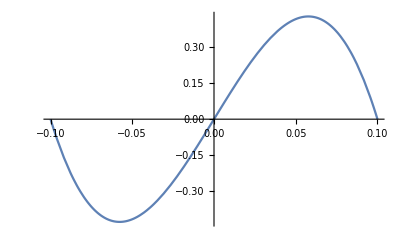

```mathematica
Plot[I*(HerDf1d[x,-1]),{x,-0.1,0.1},PlotRange->All]
```

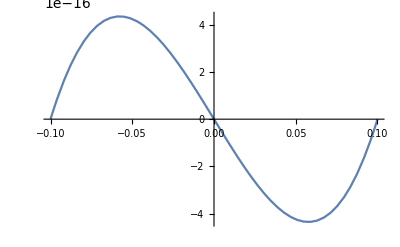

```mathematica
Plot[I*(deEerDfd[x,-1]),{x,-0.1,0.1},PlotRange->All]
```

```mathematica
Hdgfnd2[x_,t_]:=Hdgf1d[x,t]+dHdgfd[x,t];
Herfnd2[x_,t_]:=Herf1d[x,t]+dHerfd[x,t];
Edgfnd2[x_,t_]:=Edgf1d[x,t]+dEdgfd[x,t];
Eerfnd2[x_,t_]:=Eerf1d[x,t]+dEerfd[x,t];
```

```mathematica
pHdgd2[x_,t_]:=pCoe*Hdgfnd2[x,-t];
pHerd2[x_,t_]:=pCoe*Herfnd2[x,-t];
pEdgd2[x_,t_]:=pCoe*copd*Edgfnd2[x,-t];
pEerd2[x_,t_]:=pCoe*copd*Eerfnd2[x,-t];
```

```mathematica
pHdn=Show[Plot3D[pHdgd2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[pHerd2[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["H_d",Black,30,FontFamily->Times],Scaled[{1.16,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
pEdn=Show[Plot3D[pEdgd2[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],Plot3D[Re[pEerd2[x,t]],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["x",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.42,-0.22,0.1}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],280Degree],Scaled[{-0.18,-0.1,0.65}]]],Graphics3D[Text[Style["E_d",Black,30,FontFamily->Times],Scaled[{1.18,0,0.6}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

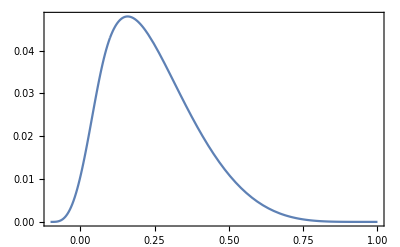
-Graphics-H_dx

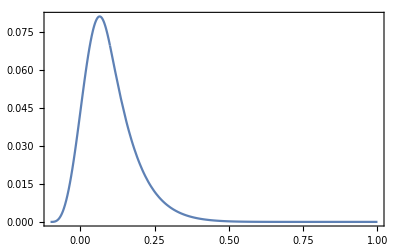
-Graphics-E_dx

```mathematica
pHd2dn=Labeled[Show[Plot[pHdgd2[x,1],{x,0.1,1},PlotRange->All],Plot[pHerd2[x,1],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"H_d",
"x"},{Left,Bottom},LabelStyle->24]
pEd2dn=Labeled[Show[Plot[pEdgd2[x,1],{x,0.1,1},PlotRange->All],Plot[Re[pEerd2[x,1]],{x,-0.1,0.1},PlotRange->All],Frame->True,FrameStyle->Directive[Thick,20]],
{"E_d",
"x"},{Left,Bottom},LabelStyle->24]
```

```mathematica
pathH2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H3d-b-noD.pdf"}];
Export[pathH2,pHdn]


pathE2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E3d-b-noD.pdf"}];
Export[pathE2,pEdn]


pathH2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"H2d-b-noD.pdf"}];
Export[pathH2d2,pHd2dn]
pathE2d2=FileNameJoin[{"C:\\Users\\DELL\\Desktop\\73diagram",
"E2d-b-noD.pdf"}];
Export[pathE2d2,pEd2dn]
```

C:\Users\DELL\Desktop\73diagram\H3d-b-noD.pdf

C:\Users\DELL\Desktop\73diagram\E3d-b-noD.pdf

C:\Users\DELL\Desktop\73diagram\H2d-b-noD.pdf

C:\Users\DELL\Desktop\73diagram\E2d-b-noD.pdf